```mathematica
trimmedAudioData =AudioData[AudioTrim[CloudImport[,"Audio"],{1,45}] //AudioNormalize,"Real64"];
```

```mathematica
leftEarAudioData=trimmedAudioData[[1]];
rightEarAudioData =trimmedAudioData[[2]];
```

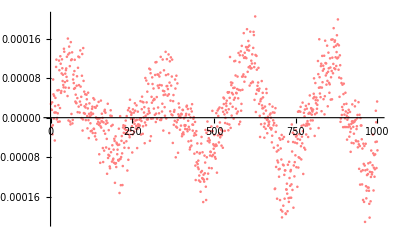

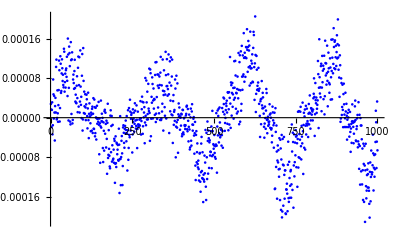

```mathematica
lp = Legended[ListPlot[leftEarAudioData[[1;;1000]], PlotStyle->Pink],"Left Ear"]
rp = Legended[ListPlot[leftEarAudioData[[1;;1000]],PlotStyle->Blue],"Right Ear"]
```

```mathematica
leah = SpectrogramArray[leftEarAudioData,Automatic, Automatic, HannWindow];
```

```mathematica
Dimensions@leah
```

{2841,2048}

```mathematica
leahA = Audio@InverseShortTimeFourier[leah, Automatic, Automatic, HannWindow]
```

```mathematica
leahMod =Audio[InverseShortTimeFourier[Transpose@MapAt[-1.5*#&,Transpose@leah,300;;600]]]
```

```mathematica
Spectrogram@leahMod
```

-Graphics-

```mathematica
Spectrogram@leahMod
```

-Graphics-

```mathematica
Spectrogram@leahMod
```

-Graphics-

```mathematica
Spectrogram@leahMod
```

-Graphics-